```mathematica
s[h_,u_,hs_,us_]:=(hs us - h u)/(hs - h);
g=1;
up[h_,hs_,us_]:=us+√(g/2(hs/h-h/hs)*(hs-h));
um[h_,hs_,us_]:=us-√(g/2(hs/h-h/hs)*(hs-h));
Manipulate[Plot[{h*up[h,hs,us],h*um[h,hs,us]},{h,0, 4},PlotRange->{-2,2}],{hs,1,3},{us,-1,1}]
```

```mathematica
hup[h_,hs_,us_]:=h us+h √(g/2(hs/h-h/hs)*(hs-h));
hum[h_,hs_,us_]:=h us-h √(g/2(hs/h-h/hs)*(hs-h));
Manipulate[Plot[{hup[h,hs,us],hum[h,hs,us]},{h,0, 4},PlotRange->{-2,2}],{hs,1,3},{us,-1,1}]
```

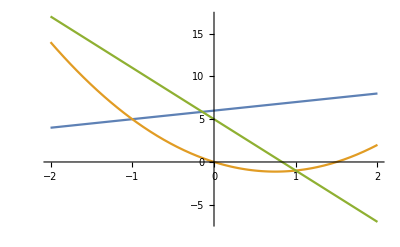

```mathematica
Plot[{6+x,2 x^2-3x,5-6x},{x,-2,2}]
```

```mathematica
Limit[(6x+4)/(√(4 x^2-x-5)),x->-Infinity]
```

-3

```mathematica
A = {{5, 3, 1},{3, 5, 3},{1, 3, 5}};
t=Eigensystem[A];
Λ=DiagonalMatrix[t[[1]]];
ql={{1},{1},{1}};
qr = {{-1},{-1},{-1}};
```

```mathematica
Λ
```

{{1/2 (11+√73),0,0},{0,4,0},{0,0,1/2 (11-√73)}}

```mathematica
t[[1]]
```

{1/2 (11+√73),4,1/2 (11-√73)}

```mathematica
ql={
```

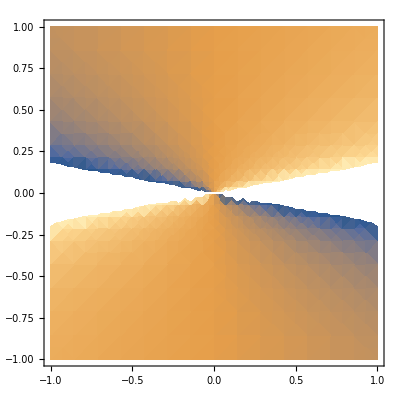

```mathematica
DensityPlot[x/t,{x,-1,1},{t,-1,1},PerformanceGoal->"Quality"]
```

```mathematica
f
```

```mathematica
??ContourPlot
```